```mathematica
data= SemanticImport["C:\\Users\\Akande\\Downloads\\Popular_Baby_Names.csv"];
```

```mathematica
baby=data;
```

```mathematica
baby//Dimensions
```

{69214,6}

```mathematica
TextCell@"The dataset consists of the following columns:
Year of Birth – The birth year of babies.
Gender – The gender of the baby (Male/Female).
Ethnicity – The ethnic background of the baby.
Child's First Name – The given first name of the baby.
Count – The number of babies given that specific name in a particular year and ethnicity.
Rank – The popularity rank of the name within that group (1 being the highest and 100 being the lowest).
The dataset provides insights into baby-naming trends over time, helping analyze how name preferences vary by ethnicity and gender."
```

The dataset consists of the following columns:
Year of Birth – The birth year of babies.
Gender – The gender of the baby (Male/Female).
Ethnicity – The ethnic background of the baby.
Child's First Name – The given first name of the baby.
Count – The number of babies given that specific name in a particular year and ethnicity.
Rank – The popularity rank of the name within that group (1 being the highest and 100 being the lowest).
The dataset provides insights into baby-naming trends over time, helping analyze how name preferences vary by ethnicity and gender.

The dataset consists of the following columns:
Year of Birth – The birth year of babies.
Gender – The gender of the baby (Male/Female).
Ethnicity – The ethnic background of the baby.
Child's First Name – The given first name of the baby.
Count – The number of babies given that specific name in a particular year and ethnicity.
Rank – The popularity rank of the name within that group.
The dataset provides insights into baby-naming trends over time,helping analyze how name preferences vary by ethnicity and gender. Let me know if you need further analysis!

```mathematica
baby[[1;;6]]
```

```mathematica
Select[baby, #Gender=="MALE" && #Ethnicity=="HISPANIC"&];
```

```mathematica
GatherBy[baby, #Ethnicity&]
```

Dataset[<>]

```mathematica
TextCell@"The function GatherBy has been used above to group the dataset by the Ethnicity attribute. This allows us to isolate and analyze baby name patterns within each ethnic group individually. By doing so, we can investigate trends such as:

The most popular names within each ethnicity.

Names that appear across multiple ethnicities.

Names that are shared by both genders within an ethnicity.

Variations in name popularity across ethnic groups over time.

These insights not only reveal cultural or demographic naming preferences but also enable us to make informed predictions about the future popularity and distribution of specific names."
```

The function GatherBy has been used above to group the dataset by the Ethnicity attribute. This allows us to isolate and analyze baby name patterns within each ethnic group individually. By doing so, we can investigate trends such as:

The most popular names within each ethnicity.

Names that appear across multiple ethnicities.

Names that are shared by both genders within an ethnicity.

Variations in name popularity across ethnic groups over time.

These insights not only reveal cultural or demographic naming preferences but also enable us to make informed predictions about the future popularity and distribution of specific names.

```mathematica
hispanicData=GatherBy[Select[baby,#Ethnicity=="HISPANIC"&], #Gender&]
```

Dataset[<>]

```mathematica
TextCell@"So what we've done above is break down and analyze the data by ethnicity.

This allows us to explore how naming trends vary across different cultural backgrounds. Once we've isolated a specific ethnicity, we then separate the data by gender, enabling us to analyze male and female names independently within each ethnic group.

In the steps above,we’ve specifically selected the Hispanic baby names,including both males and females, to prepare for more focused gender-based analysis within that ethnic category."
```

So what we've done above is break down and analyze the data by ethnicity.

This allows us to explore how naming trends vary across different cultural backgrounds. Once we've isolated a specific ethnicity, we then separate the data by gender, enabling us to analyze male and female names independently within each ethnic group.

In the steps above,we’ve specifically selected the Hispanic baby names,including both males and females, to prepare for more focused gender-based analysis within that ethnic category.

```mathematica
femalehispanicData=Select[baby,#Ethnicity=="HISPANIC"&& #Gender=="FEMALE"&];
```

```mathematica
femalesorted=SortBy[femalehispanicData,#["Year Of Birth"]&];
```

```mathematica
data2011=Select[femalesorted,#["Ethnicity"]=="HISPANIC"&&#["Gender"]=="FEMALE"&&#["Year of Birth"]==2011&];
```

```mathematica
finalfemales=DeleteDuplicatesBy[data2011,#["Child's First Name"]&];
```

```mathematica
TextCell@"A Quick Process Overview of the above code:

We began by filtering the dataset to focus on female Hispanic babies, separating this subgroup from others (such as males). This filtering step allowed us to narrow our focus for more targeted analysis.

Next, we sorted the data by Year of Birth, so we could analyze naming trends chronologically. This helps us observe how name popularity evolved over time.

After organizing the data, we proceeded to clean it by removing duplicate entries based on the baby names. This ensures that each name is represented only once per analysis slice (e.g., per year), giving us a more accurate and readable visualization or summary.
"
```

A Quick Process Overview of the above code:

We began by filtering the dataset to focus on female Hispanic babies, separating this subgroup from others (such as males). This filtering step allowed us to narrow our focus for more targeted analysis.

Next, we sorted the data by Year of Birth, so we could analyze naming trends chronologically. This helps us observe how name popularity evolved over time.

After organizing the data, we proceeded to clean it by removing duplicate entries based on the baby names. This ensures that each name is represented only once per analysis slice (e.g., per year), giving us a more accurate and readable visualization or summary.

```mathematica
highrankFemales=Select[finalfemales, #Ethnicity=="HISPANIC" &&#Gender=="FEMALE" &&#Rank <20&]
```

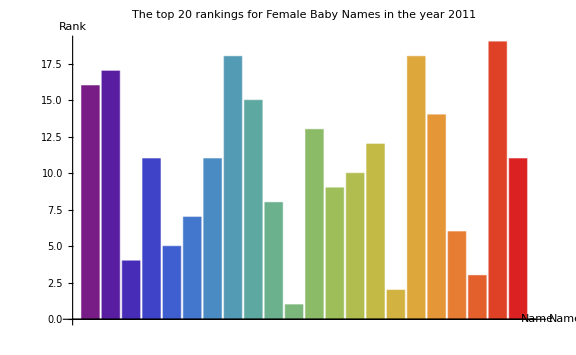

```mathematica
BarChart[Tooltip[#["Rank"],#["Child's First Name"]<>" (Rank "<>ToString[#["Rank"]]<>")"]&/@highrankFemales,ChartStyle->"Rainbow",AxesLabel->{"Name","Rank"},PlotLabel->"The top 20 rankings for Female Baby Names in the year 2011",ImageSize->Large]
```

```mathematica
lowrankFemales=Select[finalfemales, #Ethnicity=="HISPANIC" &&#Gender=="FEMALE" &&#Rank >77&]
```

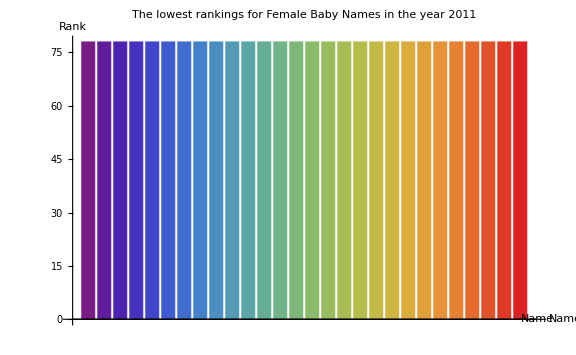

```mathematica
BarChart[Tooltip[#["Rank"],#["Child's First Name"]<>" (Rank "<>ToString[#["Rank"]]<>")"]&/@lowrankFemales,ChartStyle->"Rainbow",AxesLabel->{"Name","Rank"},PlotLabel->"The lowest rankings for Female Baby Names in the year 2011",ImageSize->Large]
```

```mathematica
TextCell@"In the analysis above, we selected female names within the top 20 rankings for the year 2011. The accompanying bar chart visually represents this data, allowing us to observe trends more clearly.

From the chart, it's evident that the most popular name for Hispanic girls in 2011 was Isabella, which ranked number one. Other highly-ranked names include Mia at number two, Sophia at number three, Ashley at number four, and Camila at number five. These names represent the top choices for Hispanic girls in 2011, based on the ranking data.

Likewise, when we do the opposite we can ascertain the lowest ranking female names which from the above bar chart is a tie between several names."
```

In the analysis above, we selected female names within the top 20 rankings for the year 2011. The accompanying bar chart visually represents this data, allowing us to observe trends more clearly.

From the chart, it's evident that the most popular name for Hispanic girls in 2011 was Isabella, which ranked number one. Other highly-ranked names include Mia at number two, Sophia at number three, Ashley at number four, and Camila at number five. These names represent the top choices for Hispanic girls in 2011, based on the ranking data.

Likewise, when we do the opposite we can ascertain the lowest ranking female names which from the above bar chart is a tie between several names.

```mathematica
data2012=Select[femalesorted,#["Ethnicity"]=="HISPANIC"&&#["Gender"]=="FEMALE"&&#["Year of Birth"]==2012&];
```

```mathematica
final2012females=DeleteDuplicatesBy[data2012,#["Child's First Name"]&];
```

```mathematica
highrank2012females= Select[final2012females, #Ethnicity=="HISPANIC"&&#Gender=="FEMALE"&&#Rank<20&];
```

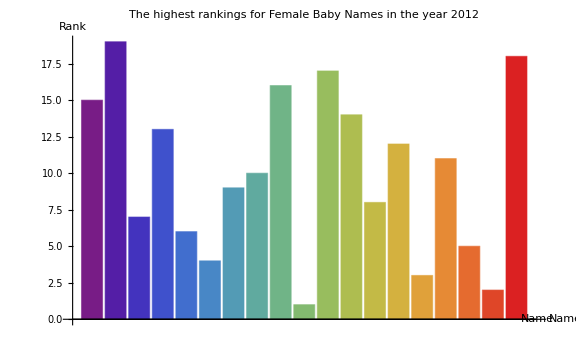

```mathematica
BarChart[Tooltip[#["Rank"],#["Child's First Name"]<>" (Rank "<>ToString[#["Rank"]]<>")"]&/@highrank2012females,ChartStyle->"Rainbow",AxesLabel->{"Name","Rank"},PlotLabel->"The highest rankings for Female Baby Names in the year 2012",ImageSize->Large]
```

```mathematica
lowrank2012females= Select[final2012females, #Ethnicity=="HISPANIC"&&#Gender=="FEMALE"&&#Rank>78&]
```

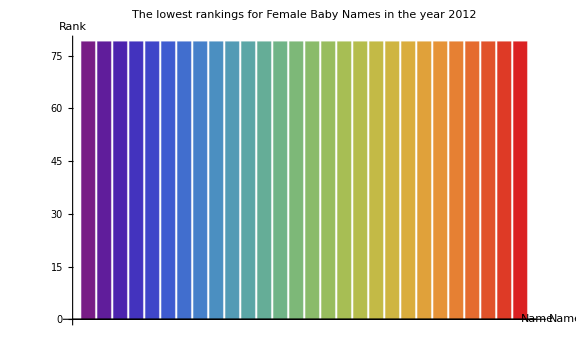

Select::normal: Nonatomic expression expected at position 1 in Select[Failure[Function, <|\"\<MessageTemplate\>\" :> StyleBox[RowBox[{\"Function\", \"::\", \"slota\"}], \"MessageName\"], \"\<MessageParameters\>\" → {\"\<YearOfBirth\>\", #Ethnicity == \"\<HISPANIC\>\" && #Gender == \"\<FEMALE\>\" && #YearOfBirth == 2011 &, <|\"\<Year of Birth\>\" → 2011, \"\<Gender\>\" → \"\<FEMALE\>\", \"\<Ethnicity\>\" → \"\<HISPANIC\>\", \"\<Child's First Name\>\" → \"\<GERALDINE\>\", \"\<Count\>\" → 13, \"\<Rank\>\" → 75|>}|>], #1[\"\<Year of Birth\>\"] == 2011 &].

Select[Failure[…],#1[Year of Birth]==2011&]

```mathematica
BarChart[Tooltip[#["Rank"],#["Child's First Name"]<>" (Rank "<>ToString[#["Rank"]]<>")"]&/@lowrank2012females,ChartStyle->"Rainbow",AxesLabel->{"Name","Rank"},PlotLabel->"The lowest rankings for Female Baby Names in the year 2012",ImageSize->Large]
```